### Start choosing the example:

```mathematica
t=25;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t];
MFGEquations=DataToEquations[Data];//Timing
```

```mathematica
v0=MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j14→0,j15→2-1,j16→1,j17→1,j18→2,j19→2-1,j20→0,j21→0,j22→0,j23→0,jt24→2-1,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→2-1,jt31→1,jt32→1,jt33→0,u34→5,u35→5,u36→6,u37→5,u38→6,u39→2-1+5,u40→5,u41→-1+6,u42→5,u43→6|>

#### Non-linear case

```mathematica
Parameters
```

<|alpha→0.8,beta→1,g[m]→Function[{m},m^beta],W[x,A]→Function[{x,A},A Sin[2 π (x+1/4)]^2],V[x]→Function[{x$},W$3246[x$,A]],H[x,p,m]→Function[{x$,p$,m$},p$^2/(2 m$^alpha)+V$3246[x$]-g$3246[m$]]|>

```mathematica
nsol1=FixedPoint[FixedSolverStepX1[MFGEquations], MFGEquations["criticalreduced1"][[2]],6, SameTest-> (Norm[(KeySort@#1-KeySort@#2)//Values]<10^(-3)&)]
```

First::nofirst: {} has zero length and no first element.

AssociateTo::invlb: The argument First[{}] is not a list, Rule, or Association.

ReplaceAll::reps: {First[{}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$Aborted

```mathematica
nsol2=FixedPoint[FixedSolverStepX2[MFGEquations], MFGEquations["criticalreduced2"][[2]],6, SameTest-> (Norm[(KeySort@#1-KeySort@#2)//Values]<10^(-3)&)]
```

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j14-j19-u34+u39==0.0517992&&j16-j21-u36+u41==-0.0517992

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j14-j19-u34+u39==0.0517992&&j16-j21-u36+u41==-0.0517992

<|j18→2.,u40→5,u42→5,j14→0.,j15→2.-1. 1.,j17→0.+1. 1.,j19→2.-1. 1.,j20→0.,j21→0.,j22→0.,j23→0.,jt24→2.-1. 1.,jt25→0.,jt26→0.,jt27→0.,jt28→0.,jt29→0.,jt30→2.-1. 1.,jt31→0.+1. 1.,jt32→0.+1. 1.,jt33→0.,u35→5,u37→5,u39→2.0518-1. 1.+1. 5.,u41→-0.0517992-1. 1.+1. 6.0518,u43→6.0518,j16→1.,u34→5.,u36→6.0518,u38→6.0518|>

```mathematica
v2=Values@KeySort@nsol2
```

{0.,1.,1.,1.,2.,1.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,1.,1.,1.,0.,5.,5,6.0518,5,6.0518,6.0518,5,5.,5,6.0518}

```mathematica
nsol3=FixedPoint[FixedSolverStepX3[MFGEquations], MFGEquations["criticalreduced2"][[2]],10, SameTest-> (Norm[(KeySort@#1-KeySort@#2)//Values]<10^(-14)&)]
```

FixedX3: next step: j14-j19-u34+u39==0.0517992&&j16-j21-u36+u41==-0.0517992

FixedX3: next step: j14-j19-u34+u39==0.0517992&&j16-j21-u36+u41==-0.0517992

<|j18→2.,u40→5,u42→5,j14→0.,j15→2.-1. 1.,j17→0.+1. 1.,j19→2.-1. 1.,j20→0.,j21→0.,j22→0.,j23→0.,jt24→2.-1. 1.,jt25→0.,jt26→0.,jt27→0.,jt28→0.,jt29→0.,jt30→2.-1. 1.,jt31→0.+1. 1.,jt32→0.+1. 1.,jt33→0.,u35→5,u37→5,u39→2.0518-1. 1.+1. 5.,u41→-0.0517992-1. 1.+1. 6.0518,u43→6.0518,j16→1.,u34→5.,u36→6.0518,u38→6.0518|>

```mathematica
nsol3n=FixedPoint[FixedSolverStepX3[MFGEquations], MFGEquations["criticalreduced2"][[2]],10, SameTest->(Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<10^(-17)&)]
```

FixedX3: next step: j14-j19-u34+u39==0.0517992&&j16-j21-u36+u41==-0.0517992

FixedX3: next step: j14-j19-u34+u39==0.0517992&&j16-j21-u36+u41==-0.0517992

FixedX3: next step: j14-j19-u34+u39==0.0517992&&j16-j21-u36+u41==-0.0517992

«7 more identical outputs»

<|j18→2.,u40→5,u42→5,j14→0.,j15→2.-1. 1.,j17→0.+1. 1.,j19→2.-1. 1.,j20→0.,j21→0.,j22→0.,j23→0.,jt24→2.-1. 1.,jt25→0.,jt26→0.,jt27→0.,jt28→0.,jt29→0.,jt30→2.-1. 1.,jt31→0.+1. 1.,jt32→0.+1. 1.,jt33→0.,u35→5,u37→5,u39→2.0518-1. 1.+1. 5.,u41→-0.0517992-1. 1.+1. 6.0518,u43→6.0518,j16→1.,u34→5.,u36→6.0518,u38→6.0518|>

```mathematica
Norm[(MFGEquations["Nrhs"]-MFGEquations["Nlhs"])/.nsol3n]
```

3.14018×10^-16

### What is this plot for?

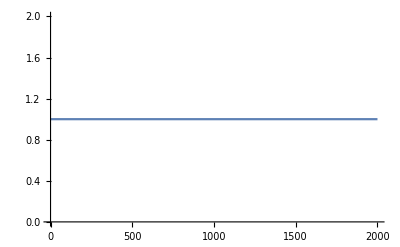
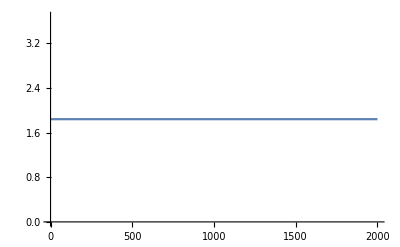
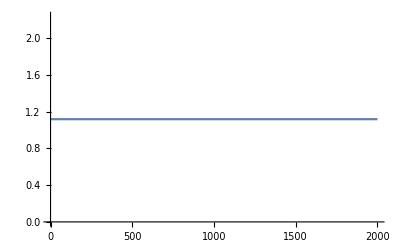
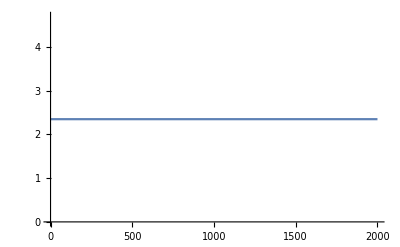
<|{2,1->2}→-Graphics-,{ex746,1->ex746}→-Graphics-,{3,2->3}→-Graphics-,{ex747,3->ex747}→-Graphics-,{2,en745->2}→-Graphics-,{1,1->2}→-Graphics-,{1,1->ex746}→-Graphics-,{2,2->3}→-Graphics-,{3,3->ex747}→-Graphics-,{en745,en745->2}→-Graphics-|>

```mathematica
Function[a,ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-a/(m^(1-alpha)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]]/@jv
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will always retrieve the most up - to - date values.